```mathematica
Exit[];
```

```mathematica
na=4;
s[i_,j_]=Piecewise[{{0,i<j}},σ[i,j]];
r[i_,j_]=Piecewise[{{1,i==j}},ρ[i,j]];
Repla=Solve[Flatten[Table[Sum[s[i,j]s[k,j],{j,na}]==r[k,i],{i,na},{k,i}]],
Flatten[Table[s[i,j],{i,na},{j,i}]]][[2^na]];
```

```mathematica
Sqrt[Expand[Simplify[Sum[Sum[q[i]σ[i]s[i,j],{i,1,na}]^2,{j,1,na}]/.Repla]]]
```

√(q[1]^2 σ[1]^2+2 q[1] q[2] ρ[1,2] σ[1] σ[2]+q[2]^2 σ[2]^2+2 q[1] q[3] ρ[1,3] σ[1] σ[3]+2 q[2] q[3] ρ[2,3] σ[2] σ[3]+q[3]^2 σ[3]^2+2 q[1] q[4] ρ[1,4] σ[1] σ[4]+2 q[2] q[4] ρ[2,4] σ[2] σ[4]+2 q[3] q[4] ρ[3,4] σ[3] σ[4]+q[4]^2 σ[4]^2)

```mathematica
f=Simplify[Expand[q1^2 s1^2+q2^2 s2^2+2 r s1 s2 q1 q2/.q2->1-q1]]
```

2 q1 (r s1-s2) s2+s2^2+q1^2 (s1^2-2 r s1 s2+s2^2)

```mathematica
Simplify[{f/.q1->0,f/.q1->1,f/.Solve[D[f,q1]==0,q1][[1,1]]}]
```

{s2^2,s1^2,-((-1+r^2) s1^2 s2^2)/(s1^2-2 r s1 s2+s2^2)}

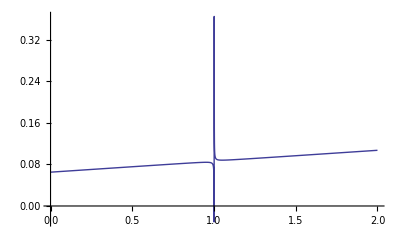

```mathematica
Plot[s1^2-((-1+r^2) s1^2 s2^2)/(s1^2-2 r s1 s2+s2^2)/.s1->0.21/.s2->0.2,{r,0,2},PlotRange->All]
```

```mathematica
s1^2-((-1+r^2) s1^2 s2^2)/(s1^2-2 r s1 s2+s2^2)/.r->1
```

s1^2